```mathematica
Get[URLDownload["https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Std01.m142"]]//Quiet;
```

C:\Users\mona_\AppData\Local\Temp\Std01-b85d182f-eac3-4edd-9ee8-bf1ad16b2928.m142        23.7.2026 10:42:12.    (135530 Bytes)

```mathematica
Clear[G,h,M,S]
```

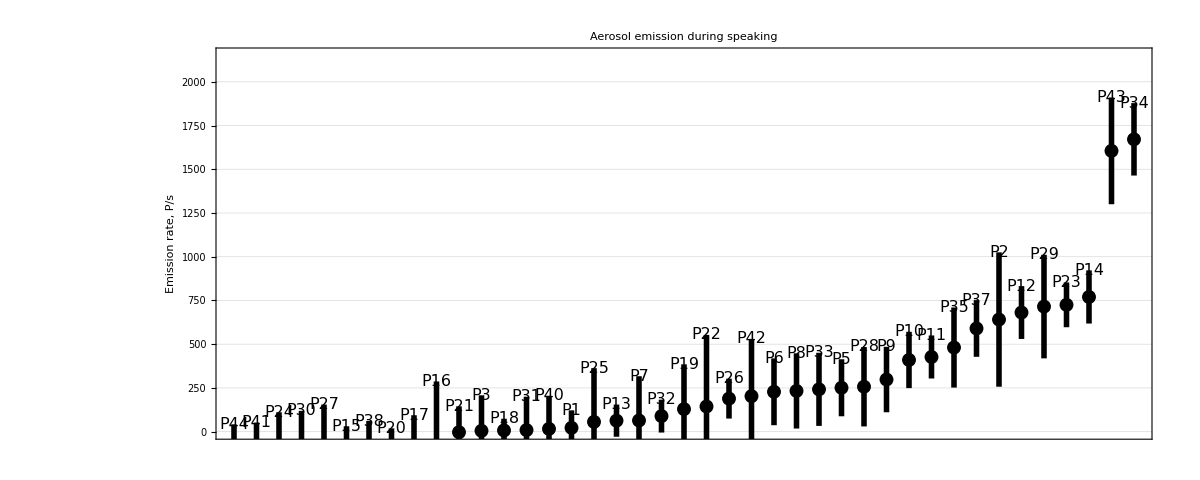

{NormalDistribution[-306.,348.],NormalDistribution[-260.,312.],NormalDistribution[-245.,356.],NormalDistribution[-175.,294.],NormalDistribution[-164.,319.],NormalDistribution[-144.,175.],NormalDistribution[-137.,198.],NormalDistribution[-121.,140.],NormalDistribution[-80.,174.],NormalDistribution[-79.,366.],NormalDistribution[-3.,148.],NormalDistribution[5.,203.],NormalDistribution[7.,67.],NormalDistribution[9.,191.],NormalDistribution[16.,189.],NormalDistribution[22.,100.],NormalDistribution[56.,307.],NormalDistribution[63.,92.],NormalDistribution[64.,253.],NormalDistribution[89.,94.],NormalDistribution[129.,256.],NormalDistribution[144.,409.],NormalDistribution[189.,114.],NormalDistribution[203.,327.],NormalDistribution[228.,191.],NormalDistribution[233.,215.],NormalDistribution[242.,209.],NormalDistribution[251.,163.],NormalDistribution[257.,227.],NormalDistribution[298.,187.],NormalDistribution[410.,161.],NormalDistribution[427.,123.],NormalDistribution[481.,229.],NormalDistribution[590.,162.],NormalDistribution[641.,384.],NormalDistribution[681.,151.],NormalDistribution[715.,296.],NormalDistribution[725.,128.],NormalDistribution[770.,152.],NormalDistribution[1605.,305.],NormalDistribution[1671.,207.]}

```mathematica
{S,G,h} = Get[URLDownload[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Fig/TaskPlots/P-s/Speaking.dat"]];
G
S
```

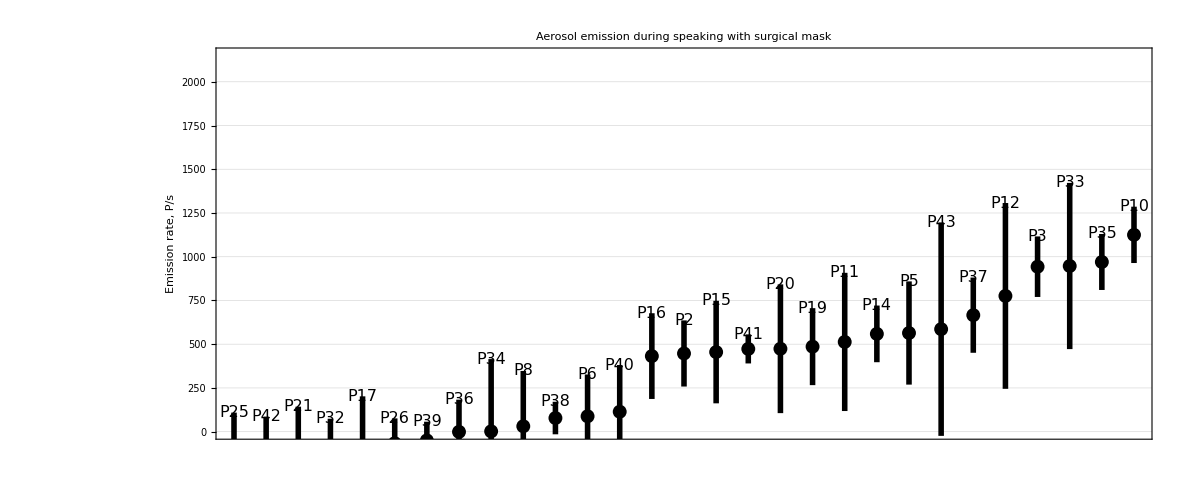

{NormalDistribution[-164.,273.],NormalDistribution[-163.,249.],NormalDistribution[-136.,279.],NormalDistribution[-122.,196.],NormalDistribution[-89.,291.],NormalDistribution[-66.,142.],NormalDistribution[-50.,107.],NormalDistribution[-1.,184.],NormalDistribution[2.,413.],NormalDistribution[31.,316.],NormalDistribution[78.,93.],NormalDistribution[88.,239.],NormalDistribution[114.,267.],NormalDistribution[432.,245.],NormalDistribution[447.,189.],NormalDistribution[455.,293.],NormalDistribution[473.,83.],NormalDistribution[474.,368.],NormalDistribution[486.,220.],NormalDistribution[513.,395.],NormalDistribution[559.,162.],NormalDistribution[564.,295.],NormalDistribution[586.,610.],NormalDistribution[666.,215.],NormalDistribution[776.,531.],NormalDistribution[943.,173.],NormalDistribution[947.,475.],NormalDistribution[970.,160.],NormalDistribution[1125.,161.]}

```mathematica
{M,G,h} = Get[URLDownload[F="https://github.com/Carl-Firle/my-data-storage/raw/refs/heads/main/data/2020_aerosol-speaking-masks/Fig/TaskPlots/P-s/Speaking%20With%20Surgical%20Mask.dat"]];
G
M
```

```mathematica
M = First/@M
S = First/@S
```

{-164.,-163.,-136.,-122.,-89.,-66.,-50.,-1.,2.,31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}

{-306.,-260.,-245.,-175.,-164.,-144.,-137.,-121.,-80.,-79.,-3.,5.,7.,9.,16.,22.,56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.,1605.,1671.}

```mathematica
(*    negative fit curve slopes are not physical plausible and need to be corrected to zero    *)

M = Select[M,(#>0.)&]
S = Select[S,(#>0.)&]
```

{2.,31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}

{5.,7.,9.,16.,22.,56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.,1605.,1671.}

```mathematica
(*    emission rates below 25 P/s produce respiratory particle concentrations too low to distinguish them from background signal    *)

M = Select[M,(#>=25.)&]
S = Select[S,(#>=25.)&]
```

{31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}

{56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.,1605.,1671.}

```mathematica
S = Select[S,(#<1500.)&]                                           (*    ohne P34 und P43    *)
```

{56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.}

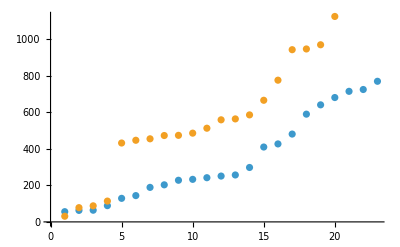

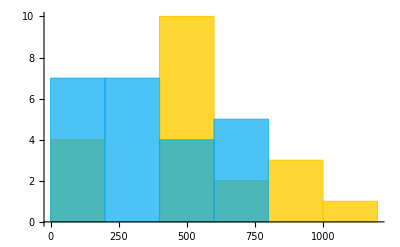

```mathematica
ListPlot[{S,M}]                       (*    ohne Maske: blau, mit Maske: orange    *)
Histogram[{M,S}]                       (*    ohne Maske: blau, mit Maske: orange    *)
```

```mathematica
MannWhitneyUStat[S,M]                                                              (*    von Oliver    *)
MannWhitneyUStat[M,S]
```

MannWhitneyUStat[{56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.},{31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.}]

MannWhitneyUStat[{31.,78.,88.,114.,432.,447.,455.,473.,474.,486.,513.,559.,564.,586.,666.,776.,943.,947.,970.,1125.},{56.,63.,64.,89.,129.,144.,189.,203.,228.,233.,242.,251.,257.,298.,410.,427.,481.,590.,641.,681.,715.,725.,770.}]

```mathematica
α = 0.05;
```

```mathematica
MannWhitneyTest[{S,M},0,"TestData",SignificanceLevel->α]                            (*    Mathematica built-in    *)
MannWhitneyTest[{M,S},0,"TestData",SignificanceLevel->α]
```

{151.,0.0528966}

{151.,0.0559513}

```mathematica
MannWhitneyTest[{S,M},0,"ShortTestConclusion",SignificanceLevel->α]                            (*    Mathematica built-in    *)
MannWhitneyTest[{M,S},0,"ShortTestConclusion",SignificanceLevel->α]
```

Do not reject

Do not reject